## Functions and exports

```mathematica
Needs["CoolTools`"]
Needs["Carlos`"]
Needs["Quantum`"]
Needs["ThesisTools`"]
SetDirectory["/home/acastillo/Documents/tesis-adan/code"];
```

```mathematica
PNGSetToGif[set_,name_]:=Export["../figures/"<>name<>".gif",
Flatten[{set, Table[set[[i]], {i, Length[set]}]}]];

l[r_,p_,lo_,up_,st_]:=First@LagrangeMultFromZCoord[
	RzLambdaTable[p,lo,up,st],
	r];
```

## SWAP Dynamics

```mathematica
x1[t]/.s[[1]]
```

InterpolatingFunction[…][t]

```mathematica
unit=MatrixExp[-I*PauliMatrix[3]*t];
vec={x,y,z};
rho0=(IdentityMatrix[2]+vec.Rest[gellMannBasis[1]])/2;
(rho0+unit.rho0.Dagger[unit])/2//FullSimplify//MatrixForm
```

(1/4 (1+ⅇ^(-2 ⅈ (t-Re[t]))) (1+z) | 1/2 ⅇ^(-ⅈ Re[t]) (x-ⅈ y) Cos[Re[t]]
1/4 (1+ⅇ^(2 ⅈ Re[t])) (x+ⅈ y) | -1/4 ⅇ^(-ⅈ Conjugate[t]) (ⅇ^(ⅈ t)+ⅇ^(ⅈ Conjugate[t])) (-1+z))

```mathematica
Inverse[{{1+Cos[t],-Sin[t],0},{Sin[t],1+Cos[t],0},{0,0,2}}/2]//FullSimplify
```

{{1,Tan[t/2],0},{-Tan[t/2],1,0},{0,0,1}}

```mathematica
Ham=Pi*(DirProd[PauliMatrix[1],PauliMatrix[1]]+DirProd[PauliMatrix[2],PauliMatrix[2]]+DirProd[PauliMatrix[3],PauliMatrix[3]])/4;
MatrixExp[-I*Ham]//FullSimplify//MatrixForm
```

(-(-1)^(3/4) | 0 | 0 | 0
0 | 0 | -(-1)^(3/4) | 0
0 | -(-1)^(3/4) | 0 | 0
0 | 0 | 0 | -(-1)^(3/4))

## MaxEnt Construction

```mathematica
(*There are two basic parameters for the coarse graining problem.
The norm of the Bloch vector and the swap probability*)
r= 0.8;
sp= 0.6;
ztargetstate=(IdentityMatrix[2]+r*PauliMatrix[3])/2;

(*We then have to construct the maximum entropy state. Since we
have acces to the rz coordinate, we obtain the lagrange mult by
numerically approximating the inverse value*)
lstep=0.002;
llow=0.;
lup=6.;
lagmult=l[r,sp,llow,lup,lstep];

ZMaxEnt=CGMaxEntStateLM[lagmult,sp];

Print["The maximum entropy state is: ", ZMaxEnt//MatrixForm]
Print["Fidelity between the coarse maximum entropy state and the target state: ", fidelity[CGKraus[ZMaxEnt,sp],ztargetstate]]
```

The maximum entropy state is: (0.793851 | 0. | 0. | 0.
0. | 0.138337 | 0. | 0.
0. | 0. | 0.0577484 | 0.
0. | 0. | 0. | 0.0100633)

Fidelity between the coarse maximum entropy state and the target state: 1.

## Numerical

```mathematica
Clear[unitary]

(*We create mixed states with a radius of zcoord, then we
obtain their corresponding MaxEnt states*)

MaxEntsNotInZ=MaxEntForStateNotInZ[#,ZMaxEnt]&/@UniformMixedStates[r,1500];

unitary[t_]:=SWAP[t];
NewMaxEnt=unitary . ZMaxEnt . Dagger[unitary[1]];
NewMaxEntsNotInZ=unitary[1] . # . Dagger[unitary[1]]&/@MaxEntsNotInZ;
CoarseMaxEntsNotInZ=Chop[CGKraus[#,sp]]&/@MaxEntsNotInZ;
CoarseNewMaxEntsNotInZ=Chop[CGKraus[#,sp]]&/@NewMaxEntsNotInZ;

PlotTwoCoarseSets[CoarseMaxEntsNotInZ,CoarseNewMaxEntsNotInZ,{"Initial states","Final states"},"Evolution of the Assignement Map"];
```

## Analytical

## CNOT Dynamics

```mathematica
CxHam=Pi*(IdentityMatrix[4]-DirProd[PauliMatrix[3],IdentityMatrix[2]]-DirProd[IdentityMatrix[2],PauliMatrix[3]]+DirProd[PauliMatrix[3],PauliMatrix[1]])/4;
(*Reconstrucción del MaxEnt*)
vec={x,y,z};
rhoA=(IdentityMatrix[2]+Tanh[pλ]*vec.Rest[gellMannBasis[1]]/r)/2;
rhoB=(IdentityMatrix[2]+Tanh[(1-p)λ]*vec.Rest[gellMannBasis[1]]/r)/2;
MaxEnt=DirProd[rhoA,rhoB];
Refine[evMaxEnt=CNOT[t].MaxEnt.Dagger[CNOT[t]],{Element[t,Reals]}];
evcoarse=Refine[CGKraus[evMaxEnt,p],{0<p<1}];
```

```mathematica
MatrixExp[-I*Pi*DirProd[PauliMatrix[3],PauliMatrix[1]]*t/4]//MatrixForm
```

(Cos[(π t)/4] | -ⅈ Sin[(π t)/4] | 0 | 0
-ⅈ Sin[(π t)/4] | Cos[(π t)/4] | 0 | 0
0 | 0 | Cos[(π t)/4] | ⅈ Sin[(π t)/4]
0 | 0 | ⅈ Sin[(π t)/4] | Cos[(π t)/4])

```mathematica
densityMatrixToPoint[{%},gellMannBasis[2]][[1]]/(2*Sqrt[2])
```

{0,0,0,0,0,0,0,0,0,0,0,0,(0.-1. ⅈ) Sin[t],0,0}

```mathematica
MatrixExp[I*Pi*DirProd[PauliMatrix[3],PauliMatrix[1]]/4]//MatrixForm
```

(1/(√2) | ⅈ/(√2) | 0 | 0
ⅈ/(√2) | 1/(√2) | 0 | 0
0 | 0 | 1/(√2) | -ⅈ/(√2)
0 | 0 | -ⅈ/(√2) | 1/(√2))

```mathematica
I*DirProd[PauliMatrix[3],PauliMatrix[1]]//MatrixForm
```

(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0)

```mathematica
CNOT[0]
```

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

## Separable Dynamics

## Step by stem evolution

#### SWAP example

```mathematica
n=2;
ti=0.0;
tf=1.0;
r= 0.8;
zstate=(IdentityMatrix[2]+r*PauliMatrix[3])/2
sp= 0.6;
(*We then have to construct the maximum entropy state. Since we
have acces to the rz coordinate, we obtain the lagrange mult by
numerically approximating the inverse value*)
lstep=0.002;
llow=0.;
lup=6.;
lagmult=l[r,sp,llow,lup,lstep];

ZMaxEnt=CGMaxEntStateLM[lagmult,sp];
MaxEntsNotInZ=MaxEntForStateNotInZ[#,ZMaxEnt]&/@UniformMixedStates[r,1500];

unitary[t_]:=SWAP[t];
NewMaxEnt=unitary . ZMaxEnt . Dagger[unitary[1]];
NewMaxEntsNotInZ=unitary[1] . # . Dagger[unitary[1]]&/@MaxEntsNotInZ;
CoarseMaxEntsNotInZ=Chop[CGKraus[#,sp]]&/@MaxEntsNotInZ;
CoarseNewMaxEntsNotInZ=Chop[CGKraus[#,sp]]&/@NewMaxEntsNotInZ;


MaxEntState=CGMaxEntStateLM[lagmult,sp];

step=(tf-ti)/n;
(*We create mixed states with a radius of r, then we
obtain their corresponding MaxEnt states*)
OriginalStates=UniformMixedStates[r,2];
MaxEnts=MaxEntAss[#,sp]&/@OriginalStates;

unitary[t_]:=SWAP[t];

Do[
MaxEntsT=unitary[step] . # . Dagger[unitary[step]]&/@MaxEnts;
CoarseStates=Chop[CGKraus[#,sp]]&/@MaxEntsT;
MaxEnts=MaxEntAss[#,sp]&/@CoarseStates;
,{i,1,n}];

PlotTwoCoarseSets[OriginalStates,CoarseStates,{"Initial states","Final states"},"Evolution of the Assignement Map"];
```

```mathematica
OriginalStates=UniformMixedStates[r,2]
MaxEnts=MaxEntAss[#,sp]&/@OriginalStates
```

{{{0.631427+0. ⅈ,0.345877+0.151974 ⅈ},{0.345877-0.151974 ⅈ,0.368573+0. ⅈ}},{{0.811214+0. ⅈ,0.0216365+0.250355 ⅈ},{0.0216365-0.250355 ⅈ,0.188786+0. ⅈ}}}

```mathematica
MaxEntForStateNotInZ[#,ZMaxEnt]&/@UniformMixedStates[r,1500]
```

## My first differential equation

### Some preliminaries, a simple example

```mathematica
Mt[t_]:=(IdentityMatrix[3]+{{Cos[2*t],-Sin[2*t],0},{Sin[2*t],Cos[2*t],0},{0,0,1}})/2; (*La evolucion no diferencial*)
incon=RandomReal[]*Normalize[Table[RandomReal[],3]]; (*Condicion incial aleatoria*)
s=NDSolve[{{x1'[t],x2'[t],x3'[t]}==H3[t].{x1[t],x2[t],x3[t]},x1[0]==incon[[1]],x2[0]==incon[[2]],x3[0]==incon[[3]]},{x1[t],x2[t],x3[t]},{t,0,π/2}]; (*evolucion diferencial*)
Plot[Norm[Mt[t].incon-{x1[t],x2[t],x3[t]}/.s],{t,0,Pi/2},PlotRange->All]
Plot[{M[t].incon,{x1[t],x2[t],x3[t]}/.s},{t,0,Pi/2},PlotRange->All,PlotLegends->Placed[{"M","Dif"},{0.8,0.7}]]
```

```mathematica
Inverse[{{1,0,0},{0,(1+Exp[-I*t])/2,0},{0,0,1}}]
```

{{1,0,0},{0,1/(1/2+ⅇ^(-ⅈ t)/2),0},{0,0,1}}

```mathematica
(*Vectorizing and devectorizing functions*)
VectorizeDO[do_]:=Flatten[do];
Devectorized[do_,shape_]:=ArrayReshape[do,shape];
shape1={2,2};
shape2={4,4};

(*Unitary, hamiltonian, rho(t), and superoperator*)
Ut=KroneckerProduct[IdentityMatrix[2],MatrixExp[-I*PauliMatrix[3]]];
Ham=KroneckerProduct[IdentityMatrix[2],PauliMatrix[3]];
rhot={{r00,r01},{r10,r11}};
Gt={{1,0,0,0},
{0,(1+Exp[-I*t])/2,0,0},
{0,0,(1+Exp[I*t])/2,0},
{0,0,0,1}};
Gtinv=Inverse[Gt]//FullSimplify;

(*Assignement map*)
Assign[do_]:=KroneckerProduct[do,do];

(*First, apply inverse dynamics to vectorized density operator, then get assmap*)
asst=Assign[Devectorized[Gtinv.VectorizeDO[rhot],shape1]]//FullSimplify;
(*Evolve the result using the unitary dynamics*)
evass=Ut.asst.Dagger[Ut]//FullSimplify;
(*Calculate the commutator with the hamiltonian*)
conm=Commutator[Ham,evass]//FullSimplify;
(*Take the CG*)
dev=(CGKraus[conm,1/2]//FullSimplify)/.(r00+r11->1);
VectorizeDO[dev]//MatrixForm
```

(0
(2 ⅇ^(-2 ⅈ) r01)/(1+ⅇ^(-ⅈ t))
-(2 ⅇ^(2 ⅈ) r10)/(1+ⅇ^(ⅈ t))
0)

```mathematica
TM={{1,0,0,1},{0,1,-I,0},{0,1,I,0},{1,0,0,-1}}/2;
MT=Inverse[TM];
rhop={1,x,y,z}
Devectorized[TM.rhop,shape1]//MatrixForm;
HP={{0,0,0,0},{0,-Tan[t],-1,0},{0,1,-Tan[t],0},{0,0,0,0}};
TM.HP.MT//FullSimplify
```

{1,x,y,z}

{{0,0,0,0},{0,-ⅈ-Tan[t],0,0},{0,0,ⅈ-Tan[t],0},{0,0,0,0}}

### Another example, an equation for the microscopic SWAP

```mathematica
H=I*MatrixLog[SWAP[1]]
```

{{0,0,0,0},{0,-π/2,π/2,0},{0,π/2,-π/2,0},{0,0,0,0}}

```mathematica
(*Vectorizing and devectorizing functions*)
VectorizeDO[do_]:=Flatten[do];
Devectorized[do_,shape_]:=ArrayReshape[do,shape];
shape1={2,2};
shape2={4,4};

(*Unitary, hamiltonian, rho(t), and superoperator*)
Ut=SWAP[t];
Ham=H;
rhot={{r00,r01},{r10,r11}};
Gt={{1,0,0,0},
{0,(1+Exp[-I*t])/2,0,0},
{0,0,(1+Exp[I*t])/2,0},
{0,0,0,1}};
Gtinv=Inverse[Gt]//FullSimplify;

(*Assignement map*)
Assign[do_]:=KroneckerProduct[do,do];

(*First, apply inverse dynamics to vectorized density operator, then get assmap*)
asst=Assign[Devectorized[Gtinv.VectorizeDO[rhot],shape1]]//FullSimplify;
(*Evolve the result using the unitary dynamics*)
evass=Ut.asst.Dagger[Ut]//FullSimplify;
(*Calculate the commutator with the hamiltonian*)
conm=Commutator[Ham,evass]//FullSimplify;
(*Take the CG*)
dev=(CGKraus[conm,1/2]//FullSimplify)/.(r00+r11->1);
VectorizeDO[dev]//MatrixForm
```

```mathematica
BoltzmannClone[rho_]:=KroneckerProduct[rho,rho];
rho={{r00,r01},{r10,r11}};
ev=Refine[SWAP[t].BoltzmannClone[rho].Dagger[SWAP[t]],{Element[t,Reals]}]//FullSimplify;
ev==BoltzmannClone[rhot]
```

True

```mathematica
SWAP[t]//MatrixForm
```

(1 | 0 | 0 | 0
0 | ⅇ^((ⅈ π t)/2) Cos[(π t)/2] | -ⅈ ⅇ^((ⅈ π t)/2) Sin[(π t)/2] | 0
0 | -ⅈ ⅇ^((ⅈ π t)/2) Sin[(π t)/2] | ⅇ^((ⅈ π t)/2) Cos[(π t)/2] | 0
0 | 0 | 0 | 1)

```mathematica
Refine[SWAP[t].BoltzmannClone[rhot].Dagger[SWAP[t]],{Element[t,Reals]}]
```

```mathematica
Depolarizing[rho_,lam_]:=(1-lam)*IdentityMatrix[2]/2+lam*rho;
rho={{r00,r01},{r10,r11}};
Depolarizing[Depolarizing[rho,1/λ],λ]//FullSimplify
```

{{r00,r01},{r10,r11}}

```mathematica
I*MatrixExp[-I*PauliMatrix[3]*Pi/2]
```

{{1,0},{0,-1}}

{{λ_3,λ_1-ⅈ λ_2},{λ_1+ⅈ λ_2,-λ_3}}

```mathematica
MaxEnt[rhovec_,p_]:=With[{vecA=MapAt[#*p*Tanh[p*λ]/r&,rhovec,{{2},{3},{4}}],vecB=MapAt[#*(1-p)*Tanh[(1-p)*λ]/r&,rhovec,{{2},{3},{4}}]},Flatten[KroneckerProduct[vecA,vecB]]];
vec={1,x,y,z};
inv[vec_,κ_]:=MapAt[#/κ&,vec,{{2},{3},{4}}]

inv[vec,κ]
psi0vec=MaxEnt[inv[vec,κ],p];
psi0=psi0vec.gellMannBasis[2]/2//FullSimplify;
```

{1,x/κ,y/κ,z/κ}

```mathematica
psit=Refine[SWAP[t].psi0.Dagger[SWAP[t]],{Element[t,Reals],Element[p,Reals]}]//FullSimplify;
```

```mathematica
conm=Commutator[I*MatrixLog[SWAP[1]],psit];
dev=CGKraus[conm,p]//FullSimplify;
```

```mathematica
change=Refine[densityMatrixToPoint[{dev},gellMannBasis[1]],{Element[t,Reals],Element[p,Reals]}][[1]]//FullSimplify;
```

```mathematica
Refine[change,{0<p<1}]//FullSimplify//MatrixForm
```

(((-0.5+1. p) ((0.-4.44288 ⅈ) p r κ (z Cos[π t]-1. x Sin[π t]) Tanh[p λ]-(0.+4.44288 ⅈ) (-1.+1. p) (-1. r x κ Sin[π t]+1. p y z Cos[π t] Tanh[p λ]) Tanh[λ-p λ]))/(r^2 κ^2)
((0.+4.44288 ⅈ) ((0.5+p (-1.5+1. p)) r y κ Sin[π t]+p x (((-0.5+(1.5-1. p) p) y+(0.5+p (-1.5+1. p)) z) Cos[π t]+(-0.5+(1.5-1. p) p) x Sin[π t]) Tanh[p λ]) Tanh[λ-p λ])/(r^2 κ^2)
(((0.+4.44288 ⅈ)+((0.-13.3286 ⅈ)+(0.+8.88577 ⅈ) p) p) r z κ Cos[(π t)/2] Sin[(π t)/2] Tanh[λ-p λ]+p y Tanh[p λ] (((0.+2.22144 ⅈ)-(0.+4.44288 ⅈ) p) r κ Cos[π t]-(0.+4.44288 ⅈ) (0.5+p (-1.5+1. p)) (y Cos[π t]+x Sin[π t]) Tanh[λ-p λ]))/(r^2 κ^2))

Missing[UnknownSymbol,Product`]

```mathematica
densityMatrixToPoint[{SWAP[1]},gellMannBasis[2]][[1]]
```

{0,0,0,0,0,0,1.41421,0,0,0,1.41421,0,0,0,1.41421}

```mathematica
Sum[LeviCivitaTensor[3][[i,j,3]],{i,3},{j,3}]
```

0

```mathematica
sumsigma=Sum[KroneckerProduct[PauliMatrix[i],PauliMatrix[i]],{i,3}]/2
```

{{1/2,0,0,0},{0,-1/2,1,0},{0,1,-1/2,0},{0,0,0,1/2}}

```mathematica
rep[mat_]:=densityMatrixToPoint[{mat},gellMannBasis[2]][[1]]/(2*Sqrt[2.])
dotpower[mat_,n_]:=Nest[#.mat&,mat,n]
```

```mathematica
dotpower[sumsigma,1]
```

{{1/4,0,0,0},{0,5/4,-1,0},{0,-1,5/4,0},{0,0,0,1/4}}

```mathematica
rep[sumsigma.sumsigma.sumsigma.sumsigma]
```

{0.,0.,0.,0.,0.,0.,-1.25,0.,0.,0.,-1.25,0.,0.,0.,-1.25}

{{0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,1.,0.,0.,0.,1.}}

```mathematica
2*Sqrt[2.]
```

2.82843

```mathematica
SWAP[t]//MatrixForm
```

(1 | 0 | 0 | 0
0 | ⅇ^((ⅈ π t)/2) Cos[(π t)/2] | -ⅈ ⅇ^((ⅈ π t)/2) Sin[(π t)/2] | 0
0 | -ⅈ ⅇ^((ⅈ π t)/2) Sin[(π t)/2] | ⅇ^((ⅈ π t)/2) Cos[(π t)/2] | 0
0 | 0 | 0 | 1)

```mathematica
densityMatrixToPoint[{SWAP[t]},gellMannBasis[2]][[1]]//MatrixForm
```

(0
0
0
0
0
0
(0.-1.41421 ⅈ) ⅇ^((ⅈ π t)/2) Sin[(π t)/2]
0
0
0
(0.-1.41421 ⅈ) ⅇ^((ⅈ π t)/2) Sin[(π t)/2]
0
0
0
1.41421-1.41421 ⅇ^((ⅈ π t)/2) Cos[(π t)/2])

```mathematica
I*densityMatrixToPoint[{MatrixLog[{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,-1}}]},gellMannBasis[2]]
```

{{0,0,2.22144+0. ⅈ,0,0,2.22144+0. ⅈ,0,0,0,0,0,0,0,0,-2.22144+0. ⅈ}}

```mathematica
H={{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,1}};
U[t_]:=MatrixExp[-I*t*H];
rho={{r00,r01},{r10,r11}};;
psi=KroneckerProduct[rho,rho];
psit=Refine[U[t].psi.Dagger[U[t]],{Element[t,Reals]}];
rhot=CGKraus[psit,1/2]//FullSimplify//MatrixForm
```

(r00 (r00+r11) | r01 (r00+ⅇ^(ⅈ t) r11)
r10 (r00+ⅇ^(-ⅈ t) r11) | r11 (r00+r11))

```mathematica
densityMatrixToPoint[{rhot},gellMannBasis[1]][[1]]//FullSimplify//MatrixForm
```

(1/2 (x (1+z)-x (-1+z) Cos[t]-y (-1+z) Sin[t])
1/2 (y (1+z)-y (-1+z) Cos[t]+x (-1+z) Sin[t])
z)

```mathematica
OBTAIN IMAGE OF THE EVOLUTION
```

```mathematica
Inverse[(IdentityMatrix[3]*(1+z)+-(z-1)*{{Cos[t],-Sin[t],0},{Sin[t],Cos[t],0},{0,0,1}})/2]//FullSimplify//MatrixForm
```

(1/(1+z-(2 z)/(1+z+Cos[t]-z Cos[t])) | -((-1+z) Sin[t])/(1+z^2+Cos[t]-z^2 Cos[t]) | 0
((-1+z) Sin[t])/(1+z^2+Cos[t]-z^2 Cos[t]) | 1/(1+z-(2 z)/(1+z+Cos[t]-z Cos[t])) | 0
0 | 0 | 1)

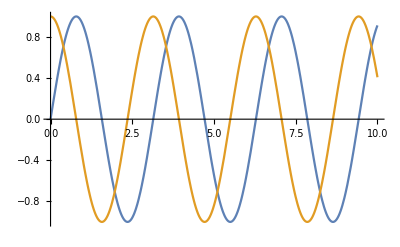

```mathematica
Plot[{Sin[2x],Cos[x]^2-Sin[x]^2},{x,0,10}]
```

## N to 1

### Local pauli_z with different frequencies

```mathematica
n=10;
μ=2;
σ=0.5;
ω=RandomVariate[NormalDistribution[μ,σ],n];
Ham=Sum[ω[[j]]*DirProd[IdentityMatrix[2^(j-1)],DirProd[PauliMatrix[3],IdentityMatrix[2^(n-j)]]],{j,1,n}];
CGNto1
```

```mathematica
??MaxEntAss
```

## Fixing my functions

```mathematica
GObsMaxEnt[p_,i_,n_]:=p*KroneckerProduct[PauliMatrix[i],IdentityMatrix[2]]+(1-p)*KroneckerProduct[IdentityMatrix[2],PauliMatrix[i]];
CGMaxEntStateLM[lambda_,p_]:=With[{ExpMat=MatrixExp[lambda*GObsMaxEnt[p,3]]},ExpMat/Tr[ExpMat]]

RadiusAsFunctionOfLagrange[l_,p_]:=Sum[p[[k]]*Tanh[p[[k]]*l],{k,1,Length[p]}];
RadiusLagrangeTable[p_,low_,up_,step_]:=Transpose[Table[{RadiusAsFunctionOfLagrange[l,p],l},{l,low,up,step}]];
LagrangeMultFromRadiusList[data_,r_]:=data[[2,NearestPosition[data[[1]],r]]]

LagrangeMultFromRadius[r_,p_,lo_:0.,up_:6.,st_:0.002]:=First@LagrangeMultFromRadiusList[
	RadiusLagrangeTable[p,lo,up,st],
	r];

MaxEntN[rho_,p_]:=With[
{vec=densityMatrixToPoint[{rho},gellMannBasis[1]][[1]]},
states=Table[(IdentityMatrix[2]+p[[k]]*Tanh[p[[k]]*LagrangeMultFromRadius[Norm[vec],p,0.,6.,0.002]*Normalize[vec].Rest[gellMannBasis[1]]])/2,{k,1,Length[p]}];
Fold[DirProd,states]];
```